```mathematica
"Skin2`QuaSK`"//Needs
```

```mathematica
q[φ_,ψ_]=ToQua[1,φ,{Sin[ψ],Cos[ψ],0}]
```

Qua[Cos[φ/2],(Sin[φ/2] Sin[ψ])/(√(Cos[ψ]^2+Sin[ψ]^2)),(Cos[ψ] Sin[φ/2])/(√(Cos[ψ]^2+Sin[ψ]^2)),0]

```mathematica
q1=q[π/3,π/3]//FullSimplify
```

Qua[(√3)/2,(√3)/4,1/4,0]

```mathematica
q1//FullSimplify
```

Qua[1/(√2),(√(3/2))/2,1/(2 √2),0]

```mathematica
q1

Rotation[q1]//FullSimplify
```

Qua[(√3)/2,(√3)/4,1/4,0]

{Angle→π/3,Axis→{(√3)/4,1/4,0}}

```mathematica
RandomVariate[NormalDistribution[]]
```

-0.131627

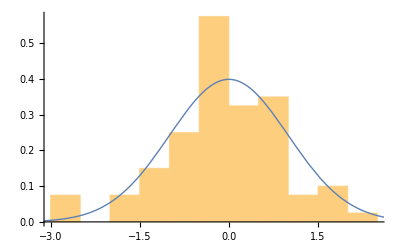

```mathematica
data=RandomVariate[NormalDistribution[0,1],80];
Show[Histogram[data,10,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},PlotStyle->Thick]]
```

```mathematica
data
```

{-0.16803,0.771543,-0.0200449,-0.44674,0.62613,0.134688,-0.563856,0.954563,-1.38732,-1.06428,0.728023,-0.330925,-1.58445,-1.67314,0.472513,-0.486088,-0.302989,-0.408184,1.68259,-0.523957,0.213198,-0.990793,-0.0275153,0.502719,0.124433,-0.529211,-0.265858,-0.30834,0.689274,-0.199158,0.431608,1.73975,-0.965395,0.346123,-1.29962,-0.133748,1.34327,0.241882,0.597028,0.373576,-1.17057,1.20821,0.293476,-0.214949,-2.79036,0.505817,0.497868,0.206995,1.1973,-0.754251,0.668563,-0.857867,-0.421566,0.740666,-0.633846,-0.148325,-0.133166,-0.835772,1.51722,-0.516225,-0.424256,-0.15826,0.170063,-0.0441041,0.59186,0.841699,0.383789,1.64206,-1.59391,0.925364,-2.96992,0.910206,-0.225292,-0.0419303,-0.0720444,-1.40177,-2.87348,-0.0431386,-1.43102,2.00707}

```mathematica
∑_(i=1)^80 data[[i]]
```

-7.15452

```mathematica
q[π/4,ψ_]
```

Qua::qmul: Please use the NonCommutativeMultiply for quaternion 
multiplication.

Indeterminate

```mathematica
Ans=q1
For[i=0,i<2,i++,
Ans=Ans**q1;
]
Ans
```

Qua[1/(√2),(√(3/2))/2,1/(2 √2),0]

Qua[-1/(√2),(√(3/2))/2,1/(2 √2),0]

```mathematica
(*Перемножение кватернионов*)
```

```mathematica
Ans=q[π/2,data[[1]]]
For[i=2,i<=3,i++,
Rotator = q[π/2,data[[i]]];
Ans=Rotator**Ans;
Print[i," ",data[[i]]];
Print[Rotator];
]
Ans
```

Qua[1/(√2),-0.118257,0.697148,0]

2 0.771543

Qua[1/(√2),0.493025,0.506879,0]

3 -0.0200449

Qua[1/(√2),-0.0141729,0.706965,0]

Qua[-0.453227,0.469848,0.752615,0.0860132]

q[π/2,data[[3]]]**q[π/2,data[[2]]]**q[π/2,data[[1]]]

Qua[-0.453227,0.469848,0.752615,0.0860132]

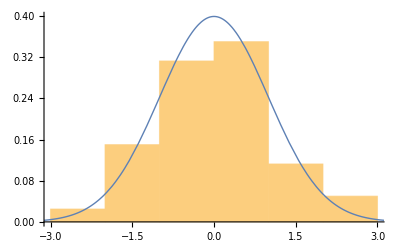

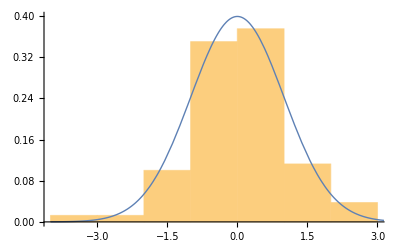

{0.623462,0.761648,-0.813659,0.101776,-0.746683,2.21331,-1.28865,-0.258957,1.23939,-0.833435,-0.729946,-0.274904,1.34103,-0.324559,-0.109329,0.53638,-0.786929,0.174747,0.850724,-0.344613,-1.70006,2.0233,-0.948442,0.30408,-0.920358,0.555503,0.176757,-1.12724,0.944965,-1.98854,0.635431,-1.0711,1.23712,0.396724,-0.760051,-2.10446,0.318114,0.248852,-0.33356,0.604595,0.595519,-1.17098,1.07695,0.884067,-0.524861,-0.0732432,-0.135585,-0.137359,1.15975,-0.224151,0.234513,-0.258891,-1.30454,-0.44354,-1.84433,0.278298,-1.16376,-2.18012,1.05455,0.648964,0.0938483,-1.66299,0.279971,0.948826,-0.378936,-0.095977,0.819713,0.280114,2.1001,-0.289563,0.530078,-0.682853,-1.1828,-1.20045,1.35497,1.10277,0.452449,2.25344,0.226921,1.07871}

0.322017

{0.125186,-0.831022,-0.857775,1.11563,-0.785019,0.915707,-0.839887,0.845523,-1.74266,0.448581,-0.931999,-0.159433,2.87198,-0.353185,-0.00466859,0.438671,2.2898,0.0697637,-0.336207,0.80082,0.17918,0.193737,-0.650034,-0.416981,-0.00603468,-0.437574,-0.746435,-0.361438,-0.644714,1.30922,2.66184,0.161404,0.805798,1.02525,-1.18665,-0.98513,0.0522601,-0.438674,-0.659707,0.159174,-0.34549,0.936154,0.94981,-1.14226,0.656482,-0.322022,-2.3752,0.0420044,-0.476552,0.135592,1.85949,-1.529,1.00114,0.33898,0.0772561,-0.841492,-1.78649,-3.57423,0.342496,0.0234679,-0.947688,-0.718002,-0.265113,-1.06308,1.59756,0.968186,-1.1668,0.587886,0.262935,0.227904,-1.76921,-0.0767788,1.15879,1.69309,0.938965,1.35118,0.66554,0.10304,0.692706,-0.502221}

0.803322

```mathematica
(*Задание углов Θ–повороты вокруг оси, Ψ–наклон оси относительно продольной оси (движение в x-y плоскости) в радианах
через нормально распеделение.
Важно правильно определить пределы для обоих распределений*)
Subscript[N, dip]=80;Subscript[ρ, hist]=6;
Θ=RandomVariate[NormalDistribution[0,1],Subscript[N, dip]];
Ψ=RandomVariate[NormalDistribution[0,1],Subscript[N, dip]];
(*Построение гистограм*)
Show[Histogram[Θ,Subscript[ρ, hist],"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->Thick]]
Show[Histogram[Ψ,Subscript[ρ, hist],"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->Thick]]
(*Чему должны быть равны суммы всех углов?*)
Θ 
∑_(i=1)^80 Θ[[i]]
Ψ
∑_(i=1)^80 Ψ[[i]]
```

```mathematica
(*Перемножение кватернионов внутри одного цикла*)
For[i=1,i<=80,i++,
Print["i = ", i,", ϕ = ",Θ[[i]],", ψ = ",Ψ[[i]]];
Rotator =q[Θ[[i]],Ψ[[i]]];
Print[Rotator];
If[i==1,
Ans=Rotator;Break,
Ans=Rotator**Ans];
]
Ans
```

i = 1, ϕ = 0.623462, ψ = 0.125186

Qua[0.951804,0.038295,0.304307,0]

i = 2, ϕ = 0.761648, ψ = -0.831022

Qua[0.928359,-0.274535,0.250561,0]

i = 3, ϕ = -0.813659, ψ = -0.857775

Qua[0.91838,0.299303,-0.258836,0]

i = 4, ϕ = 0.101776, ψ = 1.11563

Qua[0.998705,0.0456871,0.022361,0]

i = 5, ϕ = -0.746683, ψ = -0.785019

Qua[0.931114,0.257804,-0.258,0]

i = 6, ϕ = 2.21331, ψ = 0.915707

Qua[0.447657,0.709099,0.544777,0]

i = 7, ϕ = -1.28865, ψ = -0.839887

Qua[0.799507,0.44723,-0.400967,0]

i = 8, ϕ = -0.258957, ψ = 0.845523

Qua[0.991629,-0.0966204,-0.0856484,0]

i = 9, ϕ = 1.23939, ψ = -1.74266

Qua[0.814055,-0.572232,-0.0993234,0]

i = 10, ϕ = -0.833435, ψ = 0.448581

Qua[0.914422,-0.17554,-0.364715,0]

i = 11, ϕ = -0.729946, ψ = -0.931999

Qua[0.934133,0.286544,-0.212809,0]

i = 12, ϕ = -0.274904, ψ = -0.159433

Qua[0.990568,0.021753,-0.135282,0]

i = 13, ϕ = 1.34103, ψ = 2.87198

Qua[0.783503,0.165512,-0.59894,0]

i = 14, ϕ = -0.324559, ψ = -0.353185

Qua[0.986862,0.0558845,-0.151596,0]

i = 15, ϕ = -0.109329, ψ = -0.00466859

Qua[0.998506,0.000255077,-0.0546365,0]

i = 16, ϕ = 0.53638, ψ = 0.438671

Qua[0.964252,0.11255,0.239897,0]

i = 17, ϕ = -0.786929, ψ = 2.2898

Qua[0.923586,-0.288488,0.252514,0]

i = 18, ϕ = 0.174747, ψ = 0.0697637

Qua[0.996185,0.00608279,0.0870499,0]

i = 19, ϕ = 0.850724, ψ = -0.336207

Qua[0.910889,-0.136137,0.389547,0]

i = 20, ϕ = -0.344613, ψ = 0.80082

Qua[0.985192,-0.123092,-0.119353,0]

i = 21, ϕ = -1.70006, ψ = 0.17918

Qua[0.65996,-0.133899,-0.739273,0]

i = 22, ϕ = 2.0233, ψ = 0.193737

Qua[0.530464,0.163207,0.831848,0]

i = 23, ϕ = -0.948442, ψ = -0.650034

Qua[0.889649,0.276368,-0.363519,0]

i = 24, ϕ = 0.30408, ψ = -0.416981

Qua[0.988464,-0.0613396,0.138478,0]

i = 25, ϕ = -0.920358, ψ = -0.00603468

Qua[0.895973,0.00268004,-0.4441,0]

i = 26, ϕ = 0.555503, ψ = -0.437574

Qua[0.961674,-0.116188,0.24836,0]

i = 27, ϕ = 0.176757, ψ = -0.746435

Qua[0.996097,-0.0599331,0.0647953,0]

i = 28, ϕ = -1.12724, ψ = -0.361438

Qua[0.845328,0.188921,-0.49973,0]

i = 29, ϕ = 0.944965, ψ = -0.644714

Qua[0.890441,-0.2735,0.363747,0]

i = 30, ϕ = -1.98854, ψ = 1.30922

Qua[0.545114,-0.809843,-0.216805,0]

i = 31, ϕ = 0.635431, ψ = 2.66184

Qua[0.949952,0.144189,-0.277131,0]

i = 32, ϕ = -1.0711, ψ = 0.161404

Qua[0.859989,-0.0820094,-0.50368,0]

i = 33, ϕ = 1.23712, ψ = 0.805798

Qua[0.814714,0.418304,0.401576,0]

i = 34, ϕ = 0.396724, ψ = 1.02525

Qua[0.980391,0.168459,0.102254,0]

i = 35, ϕ = -0.760051, ψ = -1.18665

Qua[0.928655,0.343909,-0.139018,0]

i = 36, ϕ = -2.10446, ψ = -0.98513

Qua[0.495637,0.723784,-0.480084,0]

i = 37, ϕ = 0.318114, ψ = 0.0522601

Qua[0.987377,0.00827355,0.158171,0]

i = 38, ϕ = 0.248852, ψ = -0.438674

Qua[0.992269,-0.0527123,0.112354,0]

i = 39, ϕ = -0.33356, ψ = -0.659707

Qua[0.986124,0.101744,-0.131175,0]

i = 40, ϕ = 0.604595, ψ = 0.159174

Qua[0.954655,0.0471884,0.293951,0]

i = 41, ϕ = 0.595519, ψ = -0.34549

Qua[0.955996,-0.099355,0.276043,0]

i = 42, ϕ = -1.17098, ψ = 0.936154

Qua[0.83344,-0.445008,-0.327637,0]

i = 43, ϕ = 1.07695, ψ = 0.94981

Qua[0.858493,0.417083,0.298381,0]

i = 44, ϕ = 0.884067, ψ = -1.14226

Qua[0.903884,-0.389097,0.177757,0]

i = 45, ϕ = -0.524861, ψ = 0.656482

Qua[0.965762,-0.158338,-0.205505,0]

i = 46, ϕ = -0.0732432, ψ = -0.322022

Qua[0.99933,0.0115876,-0.0347314,0]

i = 47, ϕ = -0.135585, ψ = -2.3752

Qua[0.997703,0.0469807,0.0488014,0]

i = 48, ϕ = -0.137359, ψ = 0.0420044

Qua[0.997642,-0.00288172,-0.0685649,0]

i = 49, ϕ = 1.15975, ψ = -0.476552

Qua[0.836532,-0.25134,0.48687,0]

i = 50, ϕ = -0.224151, ψ = 0.135592

Qua[0.993726,-0.0151183,-0.110814,0]

i = 51, ϕ = 0.234513, ψ = 1.85949

Qua[0.993133,0.112146,-0.0333064,0]

i = 52, ϕ = -0.258891, ψ = -1.529

Qua[0.991634,0.128972,-0.00539391,0]

i = 53, ϕ = -1.30454, ψ = 1.00114

Qua[0.794709,-0.511138,-0.327375,0]

i = 54, ϕ = -0.44354, ψ = 0.33898

Qua[0.97551,-0.0731411,-0.20744,0]

i = 55, ϕ = -1.84433, ψ = 0.0772561

Qua[0.604098,-0.0615049,-0.794533,0]

i = 56, ϕ = 0.278298, ψ = -0.841492

Qua[0.990334,-0.10342,0.0924231,0]

i = 57, ϕ = -1.16376, ψ = -1.78649

Qua[0.835431,0.53686,0.117629,0]

i = 58, ϕ = -2.18012, ψ = -3.57423

Qua[0.462432,-0.371747,0.804961,0]

i = 59, ϕ = 1.05455, ψ = 0.342496

Qua[0.864181,0.168988,0.473957,0]

i = 60, ϕ = 0.648964, ψ = 0.0234679

Qua[0.947816,0.00748131,0.31873,0]

i = 61, ϕ = 0.0938483, ψ = -0.947688

Qua[0.998899,-0.0380916,0.0273731,0]

i = 62, ϕ = -1.66299, ψ = -0.718002

Qua[0.673771,0.486135,-0.556512,0]

i = 63, ϕ = 0.279971, ψ = -0.265113

Qua[0.990218,-0.0365591,0.134654,0]

i = 64, ϕ = 0.948826, ψ = -1.06308

Qua[0.889561,-0.399193,0.222096,0]

i = 65, ϕ = -0.378936, ψ = 1.59756

Qua[0.982105,-0.188269,0.00504036,0]

i = 66, ϕ = -0.095977, ψ = 0.968186

Qua[0.998849,-0.0395206,-0.0271892,0]

i = 67, ϕ = 0.819713, ψ = -1.1668

Qua[0.917178,-0.366399,0.15664,0]

i = 68, ϕ = 0.280114, ψ = 0.587886

Qua[0.990208,0.0774223,0.116163,0]

i = 69, ϕ = 2.1001, ψ = 0.262935

Qua[0.497529,0.225463,0.837634,0]

i = 70, ϕ = -0.289563, ψ = 0.227904

Qua[0.989537,-0.0325972,-0.140545,0]

i = 71, ϕ = 0.530078, ψ = -1.76921

Qua[0.965082,-0.256808,-0.0516324,0]

i = 72, ϕ = -0.682853, ψ = -0.0767788

Qua[0.942278,0.0256827,-0.333845,0]

i = 73, ϕ = -1.1828, ψ = 1.15879

Qua[0.830162,-0.510868,-0.22326,0]

i = 74, ϕ = -1.20045, ψ = 1.69309

Qua[0.825209,-0.560609,0.0689018,0]

i = 75, ϕ = 1.35497, ψ = 0.938965

Qua[0.779153,0.505822,0.370223,0]

i = 76, ϕ = 1.10277, ψ = 1.35118

Qua[0.851801,0.511282,0.114129,0]

i = 77, ϕ = 0.452449, ψ = 0.66554

Qua[0.97452,0.138502,0.176431,0]

i = 78, ϕ = 2.25344, ψ = 0.10304

Qua[0.429626,0.0928813,0.898218,0]

i = 79, ϕ = 0.226921, ψ = 0.692706

Qua[0.99357,0.072303,0.0871229,0]

i = 80, ϕ = 1.07871, ψ = -0.502221

Qua[0.858039,-0.247226,0.450165,0]

Qua[0.333273,0.939644,0.0564751,0.0529911]

```mathematica
(*Проверка умножения*)
```

```mathematica
q[Θ[[4]],Ψ[[4]]]**q[Θ[[3]],Ψ[[3]]]**q[Θ[[2]],Ψ[[2]]]**q[Θ[[1]],Ψ[[1]]]
```

Qua[0.942909,0.105329,0.315041,0.0240347]